## Formulate first 3 order of basis funcitons

```mathematica
phi0[x_] :=Exp[x]
phi1[x_] := (Exp[x]-1)/x
phi2[x_] := (phi1[x]-1)/x
phi3[x_] := (phi2[x]-1/2)/ x
```

## Calculate the coefficient of ETKRK4

```mathematica
a21[x_] := phi1[x/2]/2
a32[x_] := phi1[x/2]/2
a41[x_] := 1/2 phi1[x/2](phi0[x/2]-1)
a43[x_] := phi1[x/2]
b1[x_] := phi1[x]-3phi2[x]+4phi3[x]
b2[x_] := 2phi2[x]-4phi3[x]
b4[x_] :=4phi3[x]-phi2[x]
```

### Verify the order condition of the embedded scheme

```mathematica
Series[a43[x]/2,{x,0,5}]
```

1/2+x/8+x^2/48+x^3/384+x^4/3840+x^5/46080+O[x]^6

```mathematica
Series[b2[x]/2 + b2[x]/2 + b4[x], {x, 0, 5}]
```

1/2+x/6+x^2/24+x^3/120+x^4/720+x^5/5040+O[x]^6

```mathematica
Series[a41[x] + a43[x], {x, 0, 5}]
```

1+x/2+x^2/6+x^3/24+x^4/120+x^5/720+O[x]^6

```mathematica
Series[b1[x] + 2b2[x] + b4[x], {x, 0, 5}]
```

1+x/2+x^2/6+x^3/24+x^4/120+x^5/720+O[x]^6

```mathematica
Series[a43[x]/4,{x,0,5}]
```

1/4+x/16+x^2/96+x^3/768+x^4/7680+x^5/92160+O[x]^6

```mathematica
Series[b2[x]/4 + b2[x]/4 + b4[x], {x, 0, 5}]
```

1/3+x/12+x^2/60+x^3/360+x^4/2520+x^5/20160+O[x]^6

## Calculate the coefficients of the ETDRK4-B

```mathematica
Ba21[x_]:= phi1[x/2]/2
Ba31[x_]:= phi1[x/2]/2-phi2[x/2]
Ba32[x_]:= phi2[x/2]
Ba41[x_]:= phi1[x]-2phi2[x]
Ba43[x_] := 2phi2[x]
Bb1[x_] := phi1[x]-3phi2[x]+4phi3[x]
Bb2[x_] := 2phi2[x]-4phi3[x]
Bb4[x_] :=4phi3[x]-phi2[x]
```

```mathematica
Simplify[Bb4[x]]
```

-(4+ⅇ^x (-4+x)+3 x+x^2)/x^3

## Calculate the amplifying factor and get the stability region

```mathematica
x represents hc.   y represents h$\lambda$
```

```mathematica
NL[u_]:= (p+I q) u (* y = p + I q*)
E1[x_]:=Exp[x]
E2[x_]:=Exp[x/2]
U1[u_, x_]:= u
U2[u_,x_]:= E2[x] u + a21[x] NL[u]
U3[u_, x_] := E2[x] u + a21[x] NL[U2[u, x]]
U4[u_, x_] := E2[x] U2[u,x] + a21[x] (2NL[U3[u,x]] - NL[u])
up[u_, x_] := E1[x] u + (b1[x]NL[u] + b2[x](NL[U2[u,x]]+NL[U3[u,x]]) + b4[x]NL[U4[u,x]]) 
R[u_,x_] := up[u,x] / u
```

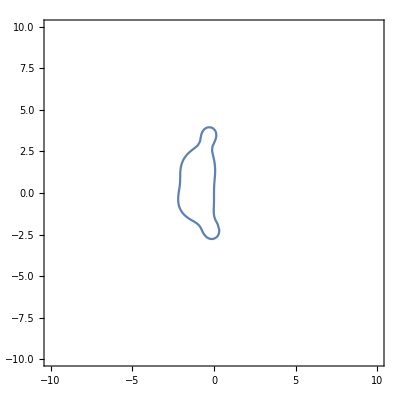

```mathematica
Am[p_, q_] := Simplify[R[u,-3 I]]
(*Am[p, q] = Abs[R[u, -1]]*)
ContourPlot[Abs[Am[p, q]]==1,{p,-10,10},{q,-10,10}]
```